## Misc. calcs for risk aversion example (Figure 9.6)

```mathematica
Clear["Global`*"];
```

```mathematica
𝒟y=TransformedDistribution[x^2,x\[Distributed]NormalDistribution[μ,σ],Assumptions->{μ>0,σ>0}]
```

TransformedDistribution[x^2,x\[Distributed]NormalDistribution[μ,σ],Assumptions→{μ>0,σ>0}]

```mathematica
py=PDF[𝒟y,x]//Simplify
```

Piecewise[{{(ⅇ^(-(√x+μ)^2/(2 σ^2)) (1+ⅇ^((2 √x μ)/σ^2)))/(2 √(2 π) √x σ), x>0}, {0, x<0}, {Indeterminate, True}}]

```mathematica
𝒟y=TransformedDistribution[x^2,x\[Distributed]NormalDistribution[μ,1]]
```

NoncentralChiSquareDistribution[1,μ^2]

```mathematica
py=PDF[𝒟y,x]
```

Piecewise[{{(ⅇ^(1/2 (-x-μ^2)) Cosh[√x μ])/(√(2 π) √x), x>0}, {0, True}}]

not sure why Mathematica could not simplify the first expression to match the second....

Anyway, plot for various values of the mean.

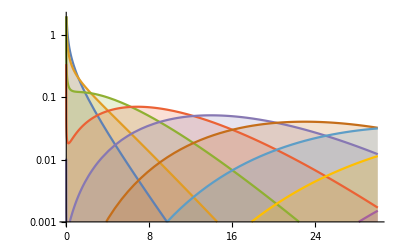

```mathematica
LogPlot[Evaluate[Table[py/.{μ->n},{n,0,8}]],{x,-1,30},PlotRange->{0.001,2},Filling->Axis]
```

```mathematica
Integrate[py,{x,0,∞}]
```

1

```mathematica
Integrate[py,{x,x0,∞},Assumptions->x0>0]
```

1/2 (Erfc[(√x0-μ)/(√2)]+Erfc[(√x0+μ)/(√2)])

```mathematica
{Mean[𝒟y],Variance[𝒟y]}
```

{1+μ^2,2+4 μ^2}

look at dimensional version:

```mathematica
pdfj=1/(√(π δj))ⅇ^(-(δj+1/2 δx^2))Cosh[√(2 δj)δx];
Integrate[pdfj,{δj,0,∞},Assumptions->{q>0,δx>0}]
```

1

```mathematica
p2big=Integrate[pdfj,{δj,δj0,∞},Assumptions->{δx>0,δj0>0}]
```

1/2 (Erfc[√δj0-δx/(√2)]+Erfc[√δj0+δx/(√2)])

```mathematica
p2big1=p2big//.{δj0->(J0-Jmin)/(Q ν^2),δx->(u+x)/ν,J0->n(1/2)(x^2(Q R)/(R+Q)+Q ν^2),Jmin->1/2 R u^2}//Simplify
```

1/2 (Erfc[-(u+x)/(√2 ν)+√((-(R u^2)/2+1/2 n ((Q R x^2)/(Q+R)+Q ν^2))/(Q ν^2))]+Erfc[(u+x)/(√2 ν)+√((-(R u^2)/2+1/2 n ((Q R x^2)/(Q+R)+Q ν^2))/(Q ν^2))])

```mathematica
Series[Erfc[α],{α,∞,5}]
```

ⅇ^(-α^2+O[1/α]^6) (1/(√π α)-1/(2 √π α^3)+3/(4 √π α^5)+O[1/α]^6)

plot P(J>2Jdet*) and its asymptotic expansion (leading term).  It’s pretty close!

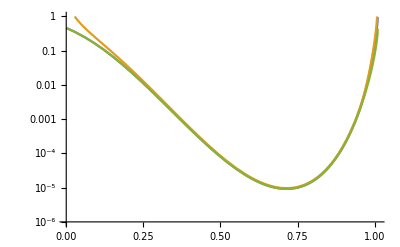

```mathematica
αminus=-(u+x)/(√2 ν)+√((-(R u^2)/2+1/2 n ((Q R x^2)/(Q+R)+Q ν^2))/(Q ν^2)); αplus=(u+x)/(√2 ν)+√((-(R u^2)/2+1/2 n ((Q R x^2)/(Q+R)+Q ν^2))/(Q ν^2));
p2big1a=1/(2 √π)((ⅇ^(-αminus^2))/αminus+(ⅇ^(-αplus^2))/αplus);  (* asymptotic approx *)
p2big1b=1/2 (Erfc[-(u+x)/(√2 ν)+√((-(R u^2)/2+1/2 n ((Q R x^2)/(Q+R)+Q ν^2))/(Q ν^2))]);  (* just drop the smaller term *)
pars={Q->1,R->1,x->1,ν->0.1,n->2,u->-u0};
LogPlot[{p2big1/.pars,p2big1a/.pars,p2big1b/.pars},{u0,0,1.5},PlotRange->{10^-6,1}]
```

```mathematica
p2big1b
```

1/2 Erfc[-(u+x)/(√2 ν)+√((-(R u^2)/2+1/2 n ((Q R x^2)/(Q+R)+Q ν^2))/(Q ν^2))]

```mathematica
Np2big1a = p2big1a/.{Q->1,R->1,x->1,ν->0.1}
```

((ⅇ^(-(-7.07107 (1+u)+10. √(0.255 n-u^2/2))^2))/(-7.07107 (1+u)+10. √(0.255 n-u^2/2))+(ⅇ^(-(7.07107 (1+u)+10. √(0.255 n-u^2/2))^2))/(7.07107 (1+u)+10. √(0.255 n-u^2/2)))/(2 √π)

```mathematica
FindRoot[D[p2big1a, u]==0/.{Q->1,R->1,x->1,ν->0.1},{u,-0.6}]
```

FindRoot::nlnum: The function value {0.282095 (-2. 2.71828^(-1. Plus[«2»]^2) (-7.07107+3./(√Plus[«2»]))-2. 2.71828^(-1. Plus[«2»]^2) (7.07107+3./(√Plus[«2»]))-(1. «1» (-«18»+«1»))/(«1»)^2-(1. 2.71828^(-1. Plus[«2»]^2) (7.07107+3./(√Plus[«2»])))/(2.82843+10. Power[«2»])^2)} is not a list of numbers with dimensions {1} at {u} = {-0.6}.

FindRoot[∂_u p2big1a==0/.{Q→1,R→1,x→1,ν→0.1},{u,-0.6}]

```mathematica
FindRoot[D[p2big1,u]==0/.{Q->1,R->1,x->1,n->2,ν->0.1},{u,-0.6}]
```

{u→-0.714143}

```mathematica
p2big1b/.pars/.u0->0.7141428428542855
```

9.22544×10^-6

```mathematica
usol=Solve[D[-(u+x)/(√2 ν)+√((-(R u^2)/2+1/2 n ((Q R x^2)/(Q+R)+Q ν^2))/(Q ν^2)),u]==0,u]//Simplify
```

{{u→-(√n Q √(Q ν^2+R (x^2+ν^2)))/(√R (Q+R))},{u→(√n Q √(Q ν^2+R (x^2+ν^2)))/(√R (Q+R))}}

```mathematica
usol1=u/.usol/.pars
```

{-0.714143,0.714143}

```mathematica
p2big1b/.u->-(√n Q x)/(Q+R)//Simplify
```

1/2 Erfc[(((-1+(√n Q)/(Q+R)) x)/ν+√((n (Q^2 ν^2+2 Q R ν^2+R^2 (x^2+ν^2)))/((Q+R)^2 ν^2)))/(√2)]

```mathematica
(-x/ν+(√n Q √(Q ν^2+R (x^2+ν^2)))/(√R (Q+R) ν)+√((n R (Q ν^2+R (x^2+ν^2)))/((Q+R)^2 ν^2)))/(√2)/.pars
```

3.02844

```mathematica
(((-1+(√n Q)/(Q+R)) x)/ν+√((n (Q^2 ν^2+2 Q R ν^2+R^2 (x^2+ν^2)))/((Q+R)^2 ν^2)))/(√2)/.pars
```

3.02795

```mathematica
(((-1+(√n Q)/(Q+R)) x)/ν+(R x)/((Q+R)ν)√n)/(√2)//Simplify
```

((-1+√n) x)/(√2 ν)

```mathematica
1/2 Erfc[((-1+√n) x)/(√2 ν)/.{n->2,x->1,ν->0.1}]
```

0.0000172043

this is a credible approximation (too big by factor of ~2)